MIT License
Copyright (c) 2021 Gaetana Spedalieri  gae.spedalieri@york.ac.uk

Permission is hereby granted, free of charge, to any person obtaining a copy of this software and associated documentation files (the “Software”), to deal in the Software without restriction, including without limitation the rights to use, copy, modify, merge, publish, distribute, sublicense, and/or sell copies of the Software, and to permit persons to whom the Software is furnished to do so,subject to the following conditions: The above copyright notice and this permission notice shall be included in all copies or substantial portions of the Software.

THE SOFTWARE IS PROVIDED “AS IS”, WITHOUT WARRANTY OF ANY KIND, EXPRESS OR IMPLIED, INCLUDING BUT NOT LIMITED TO THE WARRANTIES OF MERCHANTABILITY,  FITNESS FOR A PARTICULAR PURPOSE AND NONINFRINGEMENT. IN NO EVENT SHALL THE AUTHORS OR COPYRIGHT HOLDERS BE LIABLE FOR ANY CLAIM, DAMAGES OR OTHER LIABILITY, WHETHER IN AN ACTION OF CONTRACT, TORT OR OTHERWISE, ARISING FROM, OUT OF OR IN CONNECTION WITH THE SOFTWARE OR THE USE OR OTHER DEALINGS IN THE SOFTWARE.

Optimal displaced-squeezed probes

```mathematica
Quit[]
```

```mathematica
(**** check of the Pfa and Pmd ****)
```

```mathematica
gauss[z_,zm_,σ_]:=1/(σ  √(2 π))Exp[(-(z-zm)^2)/(2 σ^2)]
```

```mathematica
Simplify[∫_t^(+∞) gauss[z,zm,σ]ⅆz,σ>0]
```

1/2 (1-Erf[(t-zm)/(√2 σ)])

```mathematica
Simplify[∫_(-∞)^t gauss[z,zm,σ]ⅆz,σ>0]
```

1/2 (1+Erf[(t-zm)/(√2 σ)])

```mathematica
Erf[-x]+Erf[x]
```

0

```mathematica
(** evaluation thermal noise **)
```

```mathematica
λNUM=8 10^-7; (* 800 nm *)
Wband = 10^8;  (* 100 MHz *)
aRNUM =  1/10; (*  0.1 ; *)
(* 10 cm *)
```

```mathematica
hplanck=6.62607004 10^-34;
```

```mathematica
cLIGHT=299792458;
νfreq=cLIGHT/λNUM
```

374740572500000

```mathematica
angleVIEW = (1/10) (2 π)/360; (* 1/10 degree *)
```

```mathematica
Ωfov=N[angleVIEW^2]  (* in steradians *)
```

3.04617×10^-6

```mathematica
N[(π  λNUM)/(hplanck cLIGHT) ( 1.5 10^-1)] (* converting units for HskyDay *)
HskyDay=1.9 10^18;  (* Cloudy sky 800 nm *)
Δλ=10^-4; (* in nm - homodyne detector *)
(* Wband=10^8; (* 100 MHz homodyne detector - already defined above *)  *)
ΓR=N[Δλ Wband^-1 Ωfov aRNUM^2]
```

1.89782×10^18

3.04617×10^-20

```mathematica
nback=HskyDay ΓR
```

0.0578773

```mathematica
N[578773/10000000]
```

0.0578773

```mathematica
(**  probabilities **)
```

```mathematica
f[r_]:=(r+r^-1-2)/4
```

```mathematica
Solve[nS-f[r]==0,r]
```

{{r→1+2 nS-2 √(nS+nS^2)},{r→1+2 nS+2 √(nS+nS^2)}}

```mathematica
rmin[nS_]:=1+2 nS-2 √(nS+nS^2)
rmax[nS_]:=1+2 nS+2 √(nS+nS^2)
```

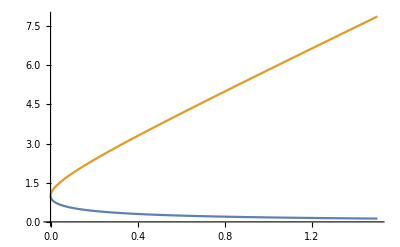

```mathematica
Plot[{rmin[nS],rmax[nS]},{nS,0,1.5}]
```

```mathematica
Ω[η_,nS_,nB_,m_,r_,t_]:=Erf[(t-m √(2 η(nS-f[r])))/(√(m (2 nB+1-η(1-r))))]
```

```mathematica
pFA[η0_,nS_,nB_,m_,r_,t_]:=1/2 (1- Ω[η0,nS,nB,m,r,t])
pMD[η1_,nS_,nB_,m_,r_,t_]:=1/2 (1+ Ω[η1,nS,nB,m,r,t])
```

```mathematica
pERR[η0_,η1_,nS_,nB_,m_,r_,t_]:=(pFA[η0,nS,nB,m,r,t]+pMD[η1,nS,nB,m,r,t])/2
```

```mathematica
zmean[η_,nS_,m_,r_]:=m √(2 η (nS-f[r]))
```

```mathematica
(** numerical/testing parameters **)
```

```mathematica
η0num=0;
η1num=2/10;
nBnum=578773/10000000;
nSnum=1/10;
mnum=10; (* testing value only *)
tnum=1; (* threshold value for test *)
N[rmin[nSnum]]
N[rmax[nSnum]]
rnum =6/10; (* squeezing for testing = 0.6 *)
N[zmean[η1num,nSnum,mnum,rnum]]
```

0.536675

1.86332

1.1547

```mathematica
N[pERR[η0num,η1num,nSnum,nBnum,mnum,rnum,tnum]]
```

0.404455

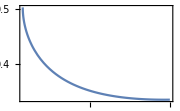

```mathematica
Plot[pERR[η0num,η1num,nSnum,nBnum,mnum,r,tnum],{r,rmin[nSnum],1},ImageSize->Small,Frame->True]
```

```mathematica
(* symmetric threshold equal to half the mean value *)
```

```mathematica
symthreshold[η0_,η1_,nS_,m_,r_]:=(zmean[η0,nS,m,r]+zmean[η1,nS,m,r])/2
```

```mathematica
tcheck=symthreshold[η0num,η1num,nSnum,mnum,1]
```

1

```mathematica
pcshom[m_,nS_,nB_,η_]:=1/2 Erfc[√((m η nS)/(4 nB+2))] (**check with previous formula for CS + hom**)
```

```mathematica
N[pERR[η0num,η1num,nSnum,nBnum,mnum,1,tcheck]]
N[pcshom[mnum,nSnum,nBnum,η1num]]
```

0.336009

0.336009

```mathematica
(** as a lidar - we see that squeezed state + hom beats  coherent state + hom **)
```

```mathematica
ϵ=1/1000; (* needed to avoid numerical problems at the border *)
tmin =ϵ;
```

```mathematica
N[zmean[η0num,nSnum,mnum,1]]
N[zmean[η1num,nSnum,mnum,1]]
```

0.

2.

```mathematica
FindMinimum[
pERR[η0num,η1num,nSnum,nBnum,mnum,r,t],{r,rmin[nSnum]+ϵ,1},{t,tmin,zmean[η1num,nSnum,mnum,1]}]
```

{0.335948,{r→0.982441,t→0.995992}}

```mathematica
(* we extract the various components below *)
```

```mathematica
pERRmin[m_]:=FindMinimum[
pERR[η0num,η1num,nSnum,nBnum,m,r,t],{r,rmin[nSnum]+ϵ,1},{t,tmin,zmean[η1num,nSnum,m,1]}]
```

```mathematica
pERRradar[m_]:=pERRmin[m][[1]]
SqueezeVALradar[m_]:=pERRmin[m][[2,1,2]]
tVALradar[m_]:=pERRmin[m][[2,2,2]]
```

```mathematica
pERRmin[mnum]
pERRradar[mnum]
SqueezeVALradar[mnum]
-10 Log10[SqueezeVALradar[mnum]]
tVALradar[mnum]
symthreshold[η0num,η1num,nSnum,mnum,SqueezeVALradar[mnum]]
```

{0.335948,{r→0.982441,t→0.995992}}

0.335948

0.982441

0.0769337

0.995992

0.999608

```mathematica
pcsHOM[m_]:=pcshom[m,nSnum,nBnum,η1num]
N[pcsHOM[mnum]]
```

0.336009

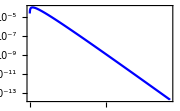

```mathematica
LogPlot[{pcsHOM[m]-pERRradar[m]},{m,1,3000},PlotStyle->{Black,Blue},ImageSize->Small,Frame->True,PlotRange->All]
```

```mathematica
(* plot of the optimal squeezing value below *)
```

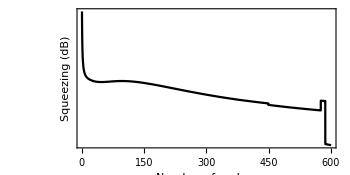

```mathematica
LogPlot[Block[{$MaxExtraPrecision=1000},N[-10Log10[SqueezeVALradar[m]],50]],{m,1,600},PlotStyle->Black,ImageSize->350,Frame->True,
FrameLabel-> {Style["Number of probes",FontSize->12,FontFamily->"Helvetica"],Style["Squeezing (dB)",FontSize->12,FontFamily->"Helvetica"]},PlotPoints->80,AspectRatio->1/2,PlotRange->All]
```

```mathematica
(* version more stable numerically below *)
```

```mathematica
SqueezeVALradarSTABLE[m_]:=FindMinimum[
Block[{$MaxExtraPrecision=1000},N[pERR[η0num,η1num,nSnum,nBnum,m,r,t],50]],{r,rmin[nSnum]+ϵ, rmax[nSnum]},{t,0,zmean[η1num,nSnum,m,1]}][[2,1,2]]
```

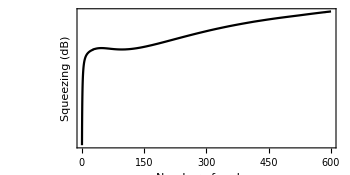

```mathematica
LogPlot[Block[{$MaxExtraPrecision=1000},N[SqueezeVALradarSTABLE[m],100]],{m,1,600},PlotStyle->Black,ImageSize->350,Frame->True,
FrameLabel-> {Style["Number of probes",FontSize->12,FontFamily->"Helvetica"],Style["Squeezing (dB)",FontSize->12,FontFamily->"Helvetica"]},PlotPoints->40,AspectRatio->1/2,PlotRange->All]
```

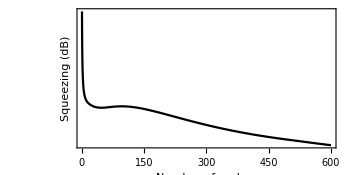

```mathematica
LogPlot[Block[{$MaxExtraPrecision=1000},N[-10Log10[SqueezeVALradarSTABLE[m]],100]],{m,1,600},PlotStyle->Black,ImageSize->350,Frame->True,
FrameLabel-> {Style["Number of probes",FontSize->12,FontFamily->"Helvetica"],Style["Squeezing (dB)",FontSize->12,FontFamily->"Helvetica"]},PlotPoints->40,AspectRatio->1/2,PlotRange->All]
```

```mathematica
(* still numerical instabilities after 600 points *)
```

```mathematica
(* check of non-monotonic behaviour in the number of probes *)
```

```mathematica
N[-10Log10[SqueezeVALradar[100]],50]
N[-10Log10[SqueezeVALradar[400]],50]
N[-10Log10[SqueezeVALradar[1300]],50]
N[-10Log10[SqueezeVALradar[2700]],50]
N[-10Log10[SqueezeVALradarSTABLE[3100]],50]
N[-10Log10[SqueezeVALradarSTABLE[3300]],50]
N[-10Log10[SqueezeVALradarSTABLE[3400]],50]
```

0.0766878

0.0757519

0.0766055

0.0754818

0.0811439

0.0765657

0.0843324

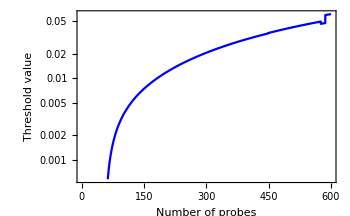

```mathematica
LogPlot[tVALradar[m]-symthreshold[η0num,η1num,nSnum,m,SqueezeVALradar[m]],{m,1,600},PlotStyle->{Black,Blue},ImageSize->350,Frame->True,
FrameLabel-> {Style["Number of probes",FontSize->12,FontFamily->"Helvetica"],Style["Threshold value",FontSize->12,FontFamily->"Helvetica"]},PlotPoints->80]
```

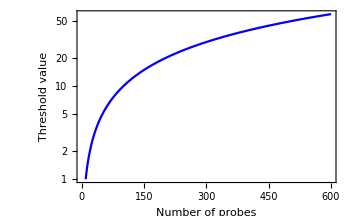

```mathematica
LogPlot[zmean[η1num,nSnum,m,1]-tVALradar[m],{m,1,600},PlotStyle->{Black,Blue},ImageSize->350,Frame->True,
FrameLabel-> {Style["Number of probes",FontSize->12,FontFamily->"Helvetica"],Style["Threshold value",FontSize->12,FontFamily->"Helvetica"]},PlotPoints->80]
```

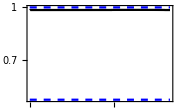

```mathematica
LogPlot[{Block[{$MaxExtraPrecision=1000},N[SqueezeVALradar[m],50]],rmin[nSnum],1},{m,1,1000},PlotStyle->{Black,{Blue,Dashed},{Blue,Dashed}},ImageSize->Small,Frame->True]
```

```mathematica
(****** Quantum reading  *****)
```

```mathematica
mnum=1000; (* redefine this parameter here to higher number *)
```

```mathematica
η0num2=90/100;
η1num2=98/100;
nBnum2=nback;
nSnum2=1;
N[rmin[nSnum2]]
N[rmax[nSnum2]]
tmin2[m_]:=zmean[η0num2,nSnum2,m,1]+ϵ
tmax2[m_]:=zmean[η1num2,nSnum2,m,1]-ϵ
```

0.171573

5.82843

```mathematica
(* below we use the more stable version where we extend the upper bound from 1 to rmax; later we check that the optimal is below 1 anyway *)
```

```mathematica
pERRvalueMIN[m_]:=FindMinimum[
pERR[η0num2,η1num2,nSnum2,nBnum2,m,r,t],{r,rmin[nSnum2]+ϵ,rmax[nSnum2]},{t,tmin2[m],tmax2[m]}]
```

```mathematica
pERRscanner[m_]:=pERRvalueMIN[m][[1]]
SqueezeVALscanner[m_]:=pERRvalueMIN[m][[2,1,2]]
```

```mathematica
pERRvalueMIN[mnum]
pERRscanner[mnum]
SqueezeVALscanner[mnum]
-10 Log10[SqueezeVALscanner[mnum]]
```

{0.437904,{r→0.385674,t→11.6827}}

0.437904

0.385674

4.1378

```mathematica
pERRscannerCS[m_]:=FindMinimum[
pERR[η0num2,η1num2,nSnum2,nBnum2,m,1,t],{t,tmin2[m],tmax2[m]}][[1]]
```

```mathematica
pERRscannerCS[mnum]
```

0.450839

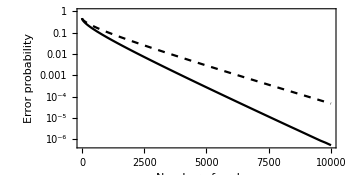

```mathematica
LogPlot[{pERRscanner[m],pERRscannerCS[m]},{m,1,10000},PlotStyle->{Black,{Black,Dashed}},ImageSize->350,Frame->True,
FrameLabel-> {Style["Number of probes",FontSize->12,FontFamily->"Helvetica"],Style["Error probability",FontSize->12,FontFamily->"Helvetica"]},AspectRatio->1/2]
```

```mathematica
(* below we check that the squeezing is <1, i.e., >0 in decibels *)
```

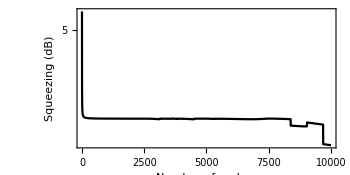

```mathematica
LogPlot[Block[{$MaxExtraPrecision=1000},N[-10 Log10[SqueezeVALscanner[m]],50]],{m,1,10000},PlotStyle->{Black},ImageSize->350,Frame->True,FrameLabel-> {Style["Number of probes",FontSize->12,FontFamily->"Helvetica"],Style["Squeezing (dB)",FontSize->12,FontFamily->"Helvetica"]},PlotPoints->40,PlotRange->All,AspectRatio->1/2]
```

```mathematica
(*** ROC ***)
```

```mathematica
FullSimplify[Solve[pFA[η0,nS,nB,m,r,t]==pf,t]]
```

{{t→(m √((2+4 nS-1/r-r) η0))/(√2)+√(m (1+2 nB+(-1+r) η0)) InverseErf[1-2 pf]}}

```mathematica
ROC[η0_,η1_,nS_,nB_,m_,r_,pf_]:=pMD[η1,nS,nB,m,r,(m √((2+4 nS-1/r-r) η0))/(√2)+√(m (1+2 nB+(-1+r) η0)) InverseErf[1-2 pf]]
```

```mathematica
mnum2=500;
```

```mathematica
ROCscan[m_,r_,pf_]:=ROC[η0num2,η1num2,nSnum2,nBnum2,m,r,pf]
```

```mathematica
ROCscan[mnum2,1,0.4]
```

0.0676163

```mathematica
ROCscanOPT[m_,pf_]:=FindMinimum[ROCscan[m,r,pf],{r,rmin[nSnum2]+ϵ,1}][[1]]
```

```mathematica
ROCscanOPT[mnum2,0.4]
```

0.0242668

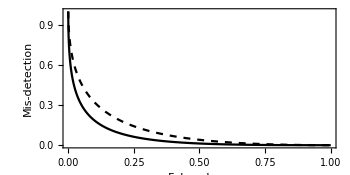

```mathematica
Plot[{ROCscanOPT[mnum2,pf],ROCscan[mnum2,1,pf]},{pf,0,1},PlotStyle->{Black,{Black,Dashed}},Frame->True,PlotRange->All,FrameLabel-> {Style["False alarm",FontSize->12,FontFamily->"Helvetica"],Style["Mis-detection",FontSize->12,FontFamily->"Helvetica"]},ImageSize->350,AspectRatio->1/2]
```